```mathematica
ClearAll["Global`*"]
```

```mathematica
xdata=Table[i,{i,-1,10,1}];
```

```mathematica
f1[x_]:=w1*x^2+w2*x+w3;
```

```mathematica
ydata=Map[f1,xdata]/.{w1->1,w2->2,w3->3};
ydataAdjusted=Table[ydata[[i]]+RandomReal[{-15,15}],{i,1,Length[ydata]}];
```

```mathematica
combodata[x_,y_]:=Table[{x[[i]],y[[i]]},{i,1,Length[x]}];
c1=combodata[xdata,ydata];
c2=combodata[xdata,ydataAdjusted];
```

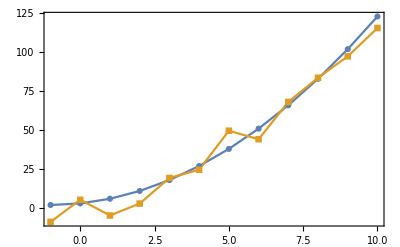

```mathematica
ListPlot[{c1,c2},Joined->{True, True},PlotMarkers->Automatic,Frame->True,Axes->False]
```

```mathematica
nlm=NonlinearModelFit[c2,f1,{w1,w2,w3},x]
```

NonlinearModelFit::nrlnum: The function value {8.84373+f1,-5.37876+f1,4.72117+f1,-2.91688+f1,-19.3599+f1,-24.6268+f1,-49.677+f1,-44.1875+f1,-68.1309+f1,-83.6551+f1,«2»} is not a list of real numbers with dimensions {12} at {w1,w2,w3} = {1.,1.,1.}.

NonlinearModelFit[{{-1,-8.84373},{0,5.37876},{1,-4.72117},{2,2.91688},{3,19.3599},{4,24.6268},{5,49.677},{6,44.1875},{7,68.1309},{8,83.6551},{9,97.411},{10,115.602}},f1,{w1,w2,w3},x]